```mathematica
SetDirectory[NotebookDirectory[]];
string = ReadString["data_en.py"];
lines = Rest[StringSplit[string, "\r\n"]];
clean = StringRiffle[StringReplace[StringDrop[lines,-1], {"senticnet"|"["|"="|"'" ->"", "]" -> "," }], "\n"];
list =ImportString[clean, "CSV"];
stringTrim[s_?StringQ] := StringTrim[s]
stringTrim[any_] := any
listclean =Map[stringTrim, list, {2}];
ruleset = #[[1]]->#[[2;;5]]&/@listclean;
```

```mathematica
data4viz =ruleset[[All,2]];
```

```mathematica
slice12 = data4viz[[All,{1,2}]];
```

```mathematica
slice13 = data4viz[[All,{1,3}]];
```

```mathematica
slice14 = data4viz[[All,{1,4}]];
```

```mathematica
slice23 = data4viz[[All,{2,3}]];
```

```mathematica
slice24 = data4viz[[All,{2,4}]];
```

```mathematica
slice34 = data4viz[[All,{3,4}]];
```

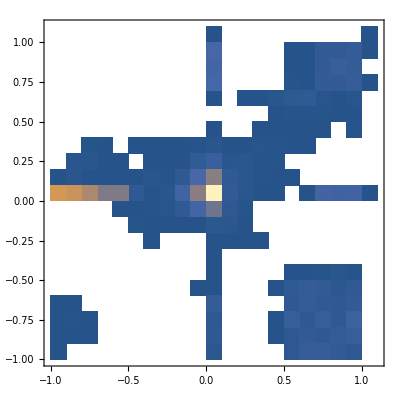
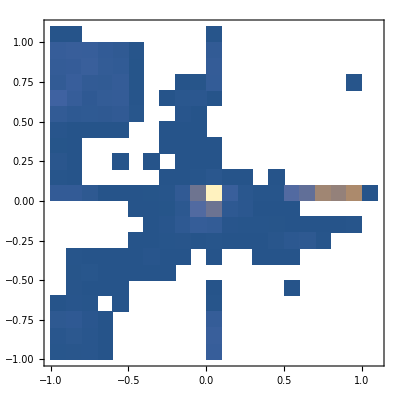
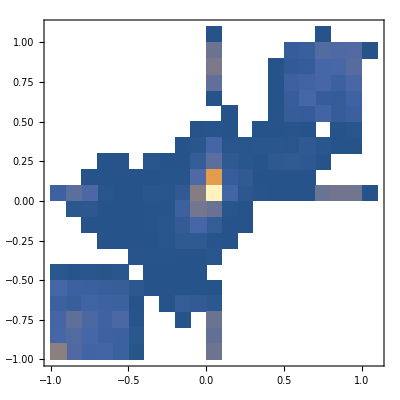
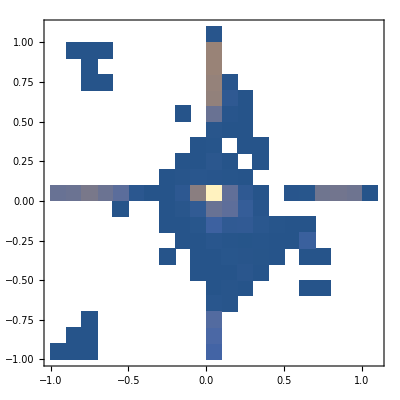
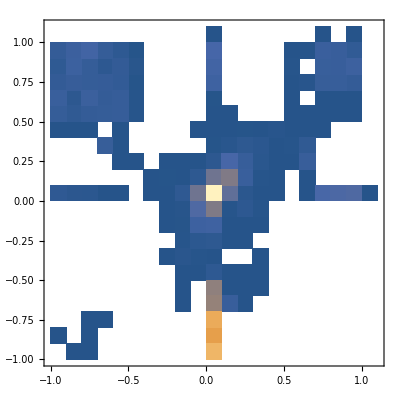
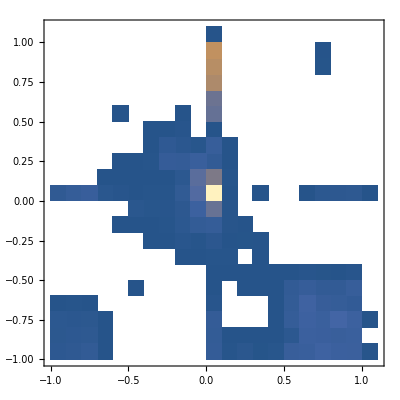

```mathematica
Table[DensityHistogram[data],{data,{slice12,slice13,slice14,slice23,slice24,slice34}}]
```

```mathematica
ruleset[[All,1]]
```

{32_teeth,a_little,a_little_hungry,a_little_specific,a_lot,a_lot_of_books,a_lot_of_energy,a_lot_of_fat,a_lot_of_flowers,a_lot_of_food,a_lot_of_fun,a_lot_of_money,a_lot_of_noise,a_lot_of_people,a_lot_of_practice,a_lot_of_sex,a_lot_of_space,a_lot_of_stress,a_lot_of_study,a_lot_of_time,a_lot_of_work,aaa,aaa_hockey,aah,abandon,abandoned_person,abandonment,abase,abasement,abash,abashed,abashment,abate,abatement,abbreviate,abc,abdicate,abdication,abdomen,abdominal_discomfort,abdominal_distension,abdominal_distention,abdominal_ectopic_gestation,abdominal_injury,abdominal_pain,abdominal_pregnancy,abdominal_tenderness,abdominoplasty,abduction,49902,zealous,zealously,zebra_crossing,zeitgeist,zenick,zenith,zenlike,zero,zero_tolerance_policy,zest,zester,zestful,zestfulness,zesty,zeus,zhuyin,zidovudine_azt,zigzag,zip,zip_code,ziploc_bag,zipper,zipper_pull,zippy,zirconium_dioxide,zit,ziziphus_mucronata,zlat,zodiacal_light,zombi,zombie,zombie_virus,zone_out,zonk_out,zoo,zooflagellate,zoologist,zoology,zoom_feature,zoom_in,zoom_ring,zoomastigote,zoophobia,zosteropidae,zostrix,zucchetto,zugzwang,zygomycosis,zymosis}
 |  |  |  |

```mathematica
With[{words = StringSplit["a_lot_of_flowers", "_"]}, Append[Insert[words,_, #]&/@Range[2, Length[words]], words]]
```

{{a,_,lot,of,flowers},{a,lot,_,of,flowers},{a,lot,of,_,flowers},{a,lot,of,flowers}}

```mathematica
StringSplit["a lot of blue flowers"]
```

{a,lot,of,blue,flowers}